```mathematica
<<Local`QFTToolKit`
```

```mathematica
varnames={t,r,w,y,z};
DeclareBaseIndices[varnames]
DeclareIndexFlavor[{red,Red}]
labs={x,δ,g,Γ};
DefineTensor[x,e,g,δ,R,G,L,Γ]
SetAttributes[L,Constant]
Clear[A]
$cmetric={{-2A[r],1,0,0,0},{1,0,0,0,0},{0,0,(r/L)^2,0,0},{0,0,0,(r/L)^2,0},{0,0,0,0,(r/L)^2}}
$metric=$cmetric//CoordinatesToTensors[varnames,x]

MapThread[SetTensorValueRules[#1,#2]&,{{g@dd[a,b],g@uu[a,b]},{$metric,Inverse[$metric]}}];
 {downΓ,upΓ}=CalculateChristoffels[labs];
MapThread[SetTensorValueRules[#1,#2]&,{{Γ@ddd[a,b,c],Γ@udd[a,b,c]},{downΓ,upΓ}}];
SelectedTensorRules[Γ@udd[_,j_,k_]/;OrderedQ[{j,k}]]//UseCoordinates[varnames,x]//TableForm;
riemannd=CalculateRiemannd[labs];
SetTensorValueRules[R@dddd[μ,ν,ρ,σ],riemannd]
(SelectedTensorRules[R@dddd[a_,b_,c_,d_]/;OrderedQ[{a,b}]∧OrderedQ[{c,d}]∧OrderedQ[{{a,b},{c,d}}]]//UseCoordinates[varnames,x]//Simplify)//TableForm;
{riemann,ricci,scalarcurvature,einstein}=CalculateRRRG[g,riemannd,Identity,Simplify[#,Trig->False]&];
SetTensorValueRules[R@uddd[μ,ν,σ,ρ],riemann]
(SelectedTensorRules[R@uddd[a_,b_,c_,d_]/;OrderedQ[{c,d}]]//UseCoordinates[varnames,x]//Simplify)//TableForm;
SetTensorValueRules[R@dd[μ,ν],ricci];
(SelectedTensorRules[R@dd[a_,b_]/;OrderedQ[{a,b}]]//UseCoordinates[varnames,x]//Simplify)//TableForm;
scalarcurvature//UseCoordinates[varnames];
SetTensorValueRules[G@dd[μ,ν],einstein];
(SelectedTensorRules[G@dd[a_,b_]/;OrderedQ[{a,b}]]//UseCoordinates[varnames,x]//Simplify)//TableForm
```

{{-2 A[r],1,0,0,0},{1,0,0,0,0},{0,0,r^2/L^2,0,0},{0,0,0,r^2/L^2,0},{0,0,0,0,r^2/L^2}}

{{-2 A[x_r^r],1,0,0,0},{1,0,0,0,0},{0,0,((x_r^r)^2)/L^2,0,0},{0,0,0,((x_r^r)^2)/L^2,0},{0,0,0,0,((x_r^r)^2)/L^2}}

G_tt^tt→-(6 A[r] (2 A[r]+r A'[r]))/r^2
G_rt^rt→(6 A[r]+3 r A'[r])/r^2
G_ww^ww→(2 A[r]+4 r A'[r]+r^2 A''[r])/L^2
G_yy^yy→(2 A[r]+4 r A'[r]+r^2 A''[r])/L^2
G_zz^zz→(2 A[r]+4 r A'[r]+r^2 A''[r])/L^2

```mathematica
Clear[A];
$=einstein+Λ $metric->0//.rr:Rule[_,_]:>Thread[rr]//Flatten//DeleteDuplicates
$ein0=$/.Rule->Equal/.Λ->-6/L^2//Simplify//DeleteCases[#,True]&//UseCoordinates[varnames,x];Column[$ein0]//Framed
$soln=DSolve[$ein0[[1]],A[r],r]//Flatten
$s=C[1]->-m L^2/2
$1=$soln[[2]]/.$s
A=Inactive[Function][r,$1[[2]]]
$=$1//Activate//Simplify
$A=A[rh]==0//Activate
$rh=Solve[$A,rh][[-1]]
$=T->A'[rh]/(2 π)//Activate;
$sT=$/.$rh
```

{-2 Λ A[x_r^r]-(6 A[x_r^r] (2 A[x_r^r]+x_r^r A'[x_r^r]))/((x_r^r)^2)→0,Λ+(6 A[x_r^r]+3 x_r^r A'[x_r^r])/((x_r^r)^2)→0,0→0,(Λ (x_r^r)^2)/L^2+(2 A[x_r^r]+4 x_r^r A'[x_r^r]+(x_r^r)^2 A''[x_r^r])/L^2→0}

6 A[r] (2/L^2-(2 A[r]+r A'[r])/r^2)==0
L ((2 A[r])/r+A'[r])==(2 r)/L
2 L A[r]+(r (4 L^2 A'[r]+r (-6+L^2 A''[r])))/L==0

{A[r]→0,A[r]→r^2/(2 L^2)+C[1]/r^2}

C[1]→-(L^2 m)/2

A[r]→-(L^2 m)/(2 r^2)+r^2/(2 L^2)

Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)]

(-L^4 m+r^4)/(2 L^2 r^2)→(-L^4 m+r^4)/(2 L^2 r^2)

-(L^2 m)/(2 rh^2)+rh^2/(2 L^2)==0

{rh→L m^(1/4)}

T→m^(1/4)/(L π)

Perturbed metric

```mathematica
varnames={t,r,w,y,z};
DeclareBaseIndices[varnames]
DeclareIndexFlavor[{red,Red}]
labs={x,δ,g,Γ};
DefineTensor[x,e,g,δ,R,G,L,Γ]
SetAttributes[L,Constant]
Clear[A]

$dg=SparseArray[{{3,4}->η Exp[I(q z - ω t)](r/L)^2f[r],{4,3}->η Exp[I(q z - ω t)](r/L)^2f[r]},{5,5}];
$cmetric={{-2A[r],1,0,0,0},{1,0,0,0,0},{0,0,(r/L)^2,0,0},{0,0,0,(r/L)^2,0},{0,0,0,0,(r/L)^2}}+$dg;
MatrixForm[$cmetric]
$metric=$cmetric//CoordinatesToTensors[varnames,x]

MapThread[SetTensorValueRules[#1,#2]&,{{g@dd[a,b],g@uu[a,b]},{$metric,Inverse[$metric]}}];
 {downΓ,upΓ}=CalculateChristoffels[labs];
MapThread[SetTensorValueRules[#1,#2]&,{{Γ@ddd[a,b,c],Γ@udd[a,b,c]},{downΓ,upΓ}}];
SelectedTensorRules[Γ@udd[_,j_,k_]/;OrderedQ[{j,k}]]//UseCoordinates[varnames,x]//TableForm;
riemannd=CalculateRiemannd[labs];
SetTensorValueRules[R@dddd[μ,ν,ρ,σ],riemannd]
(SelectedTensorRules[R@dddd[a_,b_,c_,d_]/;OrderedQ[{a,b}]∧OrderedQ[{c,d}]∧OrderedQ[{{a,b},{c,d}}]]//UseCoordinates[varnames,x]//Simplify)//TableForm;
```

(-2 A[r] | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | r^2/L^2 | (ⅇ^(ⅈ (q z-t ω)) r^2 η f[r])/L^2 | 0
0 | 0 | (ⅇ^(ⅈ (q z-t ω)) r^2 η f[r])/L^2 | r^2/L^2 | 0
0 | 0 | 0 | 0 | r^2/L^2)

{{-2 A[x_r^r],1,0,0,0},{1,0,0,0,0},{0,0,((x_r^r)^2)/L^2,(ⅇ^(ⅈ (-ω x_t^t+q x_z^z)) η f[x_r^r] (x_r^r)^2)/L^2,0},{0,0,(ⅇ^(ⅈ (-ω x_t^t+q x_z^z)) η f[x_r^r] (x_r^r)^2)/L^2,((x_r^r)^2)/L^2,0},{0,0,0,0,((x_r^r)^2)/L^2}}

```mathematica
{riemann,ricci,scalarcurvature,einstein}=CalculateRRRG[g,riemannd,Identity,Simplify[#,Trig->False]&];
SetTensorValueRules[R@uddd[μ,ν,σ,ρ],riemann]
(SelectedTensorRules[R@uddd[a_,b_,c_,d_]/;OrderedQ[{c,d}]]//UseCoordinates[varnames,x]//Simplify)//TableForm;
SetTensorValueRules[R@dd[μ,ν],ricci];
(SelectedTensorRules[R@dd[a_,b_]/;OrderedQ[{a,b}]]//UseCoordinates[varnames,x]//Simplify)//TableForm;
scalarcurvature//UseCoordinates[varnames];
SetTensorValueRules[G@dd[μ,ν],einstein];
(SelectedTensorRules[G@dd[a_,b_]/;OrderedQ[{a,b}]]//UseCoordinates[varnames,x]//Simplify)//TableForm
```

G_tt^tt→(ⅇ^(2 ⅈ q z) r^2 η^2 ω f[r]^2 (ⅇ^(2 ⅈ q z) η^2 f[r]^2 (ω-2 ⅈ A'[r])+ⅇ^(2 ⅈ t ω) (-3 ω+2 ⅈ A'[r]))+A[r] (-12 ⅇ^(4 ⅈ t ω) r A'[r]-ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (7 L^2 q^2+16 ⅈ r ω-24 r A'[r])+ⅇ^(4 ⅈ q z) η^4 f[r]^4 (3 L^2 q^2+16 ⅈ r ω-12 r A'[r])+2 ⅈ ⅇ^(4 ⅈ q z) r^2 η^4 f[r]^3 (3 ω+2 ⅈ A'[r]) f'[r]+2 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f[r] (-7 ⅈ ω+2 A'[r]) f'[r])+A[r]^2 (-24 ⅇ^(4 ⅈ t ω)-24 ⅇ^(4 ⅈ q z) η^4 f[r]^4+6 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2+f[r]^2 (48 ⅇ^(2 ⅈ (q z+t ω)) η^2+2 ⅇ^(4 ⅈ q z) r^2 η^4 f'[r]^2)+8 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (4 f'[r]+r f''[r])-8 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (4 f'[r]+r f''[r])))/(2 r^2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_tw^tw→0
G_ty^ty→0
G_tz^tz→(ⅇ^(2 ⅈ q z) q η^2 ω f[r]^2 (3 ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2))/(2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_rt^rt→(12 ⅇ^(4 ⅈ t ω) r A'[r]+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (7 L^2 q^2+12 ⅈ r ω-24 r A'[r])-3 ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^2 q^2+4 ⅈ r ω-4 r A'[r])+4 ⅈ ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f[r] (2 ω+ⅈ A'[r]) f'[r]+4 ⅇ^(4 ⅈ q z) r^2 η^4 f[r]^3 (-ⅈ ω+A'[r]) f'[r]+A[r] (24 ⅇ^(4 ⅈ t ω)+24 ⅇ^(4 ⅈ q z) η^4 f[r]^4-6 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2-2 ⅇ^(2 ⅈ q z) η^2 f[r]^2 (24 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)-8 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (4 f'[r]+r f''[r])+8 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (4 f'[r]+r f''[r])))/(4 r^2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_rr^rr→-(ⅇ^(2 ⅈ q z) η^2 (-ⅇ^(2 ⅈ t ω) r f'[r]^2-ⅇ^(2 ⅈ q z) r η^2 f[r]^2 f'[r]^2-2 ⅇ^(2 ⅈ t ω) f[r] (2 f'[r]+r f''[r])+2 ⅇ^(2 ⅈ q z) η^2 f[r]^3 (2 f'[r]+r f''[r])))/(2 r (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_rw^rw→0
G_ry^ry→0
G_rz^rz→-(ⅈ ⅇ^(2 ⅈ q z) q η^2 f[r] (-3 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) η^2 f[r]^2) f'[r])/(2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_ww^ww→(2 ⅈ ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f[r] (5 ω+4 ⅈ A'[r]) f'[r]+2 ⅇ^(4 ⅈ q z) r^2 η^4 f[r]^3 (-ⅈ ω+4 A'[r]) f'[r]+4 ⅇ^(4 ⅈ t ω) r (4 A'[r]+r A''[r])+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (5 L^2 q^2+12 ⅈ r ω-32 r A'[r]-8 r^2 A''[r])-ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^2 q^2+12 ⅈ r ω-16 r A'[r]-4 r^2 A''[r])+2 A[r] (4 ⅇ^(4 ⅈ t ω)+4 ⅇ^(4 ⅈ q z) η^4 f[r]^4-ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2+f[r]^2 (-8 ⅇ^(2 ⅈ (q z+t ω)) η^2-3 ⅇ^(4 ⅈ q z) r^2 η^4 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (3 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (3 f'[r]+r f''[r])))/(4 L^2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_wy^wy→(ⅇ^(ⅈ (q z-t ω)) η (6 ⅈ ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 ω f[r]^2 f'[r]-ⅇ^(4 ⅈ q z) η^4 f[r]^5 (L^2 q^2+6 ⅈ r ω-8 A[r]-16 r A'[r]-4 r^2 A''[r])+2 ⅇ^(2 ⅈ t ω) f[r] (A[r] (4 ⅇ^(2 ⅈ t ω)-3 ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)+ⅇ^(2 ⅈ t ω) (L^2 q^2+3 ⅈ r ω+8 r A'[r]+2 r^2 A''[r]))-ⅇ^(2 ⅈ q z) η^2 f[r]^3 (2 A[r] (8 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)+ⅇ^(2 ⅈ t ω) (-3 L^2 q^2+32 r A'[r]+8 r^2 A''[r]))+4 ⅈ ⅇ^(4 ⅈ t ω) r ((r ω+3 ⅈ A[r]+ⅈ r A'[r]) f'[r]+ⅈ r A[r] f''[r])+2 ⅇ^(4 ⅈ q z) r η^4 f[r]^4 ((-ⅈ r ω+6 A[r]+2 r A'[r]) f'[r]+2 r A[r] f''[r])))/(4 L^2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_wz^wz→0
G_yy^yy→(2 ⅈ ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f[r] (5 ω+4 ⅈ A'[r]) f'[r]+2 ⅇ^(4 ⅈ q z) r^2 η^4 f[r]^3 (-ⅈ ω+4 A'[r]) f'[r]+4 ⅇ^(4 ⅈ t ω) r (4 A'[r]+r A''[r])+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (5 L^2 q^2+12 ⅈ r ω-32 r A'[r]-8 r^2 A''[r])-ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^2 q^2+12 ⅈ r ω-16 r A'[r]-4 r^2 A''[r])+2 A[r] (4 ⅇ^(4 ⅈ t ω)+4 ⅇ^(4 ⅈ q z) η^4 f[r]^4-ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2+f[r]^2 (-8 ⅇ^(2 ⅈ (q z+t ω)) η^2-3 ⅇ^(4 ⅈ q z) r^2 η^4 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (3 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (3 f'[r]+r f''[r])))/(4 L^2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)
G_yz^yz→0
G_zz^zz→(2 ⅈ ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f[r] (7 ω+4 ⅈ A'[r]) f'[r]+2 ⅇ^(4 ⅈ q z) r^2 η^4 f[r]^3 (-3 ⅈ ω+4 A'[r]) f'[r]+4 ⅇ^(4 ⅈ t ω) r (4 A'[r]+r A''[r])+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (L^2 q^2+12 ⅈ r ω-32 r A'[r]-8 r^2 A''[r])-ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^2 q^2+12 ⅈ r ω-16 r A'[r]-4 r^2 A''[r])+2 A[r] (4 ⅇ^(4 ⅈ t ω)+4 ⅇ^(4 ⅈ q z) η^4 f[r]^4-3 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2-ⅇ^(2 ⅈ q z) η^2 f[r]^2 (8 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (3 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (3 f'[r]+r f''[r])))/(4 L^2 (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2)^2)

```mathematica
Clear[A];
SetAttributes[{η,ω,q},Constant]
$=einstein+Λ $metric->0//.rr:Rule[_,_]:>Thread[rr]//Flatten//DeleteDuplicates
$ein1=$/.Rule->Equal/.Λ->-6/L^2//Simplify//DeleteCases[#,True]&//UseCoordinates[varnames,x];Column[$ein1]//Framed
```

{-2 Λ A[x_r^r]+(2 A[x_r^r] A'[x_r^r])/x_r^r+(8 ⅇ^(4 ⅈ ω x_t^t) A[x_r^r] A'[x_r^r]+ⅇ^(4 ⅈ q x_z^z) η^2 f[x_r^r]^4 (8 η^2 A[x_r^r] A'[x_r^r]+x_r^r (η^2 ω^2-2 ⅈ η^2 ω A'[x_r^r]))-ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) f[x_r^r]^2 (16 η^2 A[x_r^r] A'[x_r^r]+x_r^r (3 η^2 ω^2-2 ⅈ η^2 ω A'[x_r^r]))-4 ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^2 A[x_r^r] f[x_r^r] x_r^r A'[x_r^r] f'[x_r^r]+4 ⅇ^(4 ⅈ q x_z^z) η^4 A[x_r^r] f[x_r^r]^3 x_r^r A'[x_r^r] f'[x_r^r])/(2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2 x_r^r)+2 A[x_r^r] A''[x_r^r]+(A[x_r^r] (2 ⅇ^(ⅈ (2 ω x_t^t+q x_z^z)) f[x_r^r] (-7 ⅈ ⅇ^(ⅈ q x_z^z) η^2 ω (x_r^r)^2 f'[x_r^r]+4 ⅇ^(ⅈ q x_z^z) η^2 (x_r^r)^2 A'[x_r^r] f'[x_r^r])+2 ⅇ^(3 ⅈ q x_z^z) η f[x_r^r]^3 (3 ⅈ ⅇ^(ⅈ q x_z^z) η^3 ω (x_r^r)^2 f'[x_r^r]-4 ⅇ^(ⅈ q x_z^z) η^3 (x_r^r)^2 A'[x_r^r] f'[x_r^r])-4 ⅇ^(4 ⅈ ω x_t^t) x_r^r (6 A'[x_r^r]+x_r^r A''[x_r^r])+ⅇ^(4 ⅈ q x_z^z) η^2 f[x_r^r]^4 (3 L^2 q^2 η^2+8 ⅈ η^2 x_r^r (2 ω+3 ⅈ A'[x_r^r])-4 η^2 (x_r^r)^2 A''[x_r^r])+ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) f[x_r^r]^2 (-7 L^2 q^2 η^2-16 ⅈ η^2 x_r^r (ω+3 ⅈ A'[x_r^r])+8 η^2 (x_r^r)^2 A''[x_r^r])-2 A[x_r^r] (12 ⅇ^(4 ⅈ ω x_t^t)+12 ⅇ^(4 ⅈ q x_z^z) η^4 f[x_r^r]^4-3 ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^2 (x_r^r)^2 f'[x_r^r]^2-ⅇ^(2 ⅈ q x_z^z) f[x_r^r]^2 (24 ⅇ^(2 ⅈ ω x_t^t) η^2+ⅇ^(2 ⅈ q x_z^z) η^4 (x_r^r)^2 f'[x_r^r]^2)-2 ⅈ ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η f[x_r^r] x_r^r (-8 ⅈ η f'[x_r^r]-2 ⅈ η x_r^r f''[x_r^r])+2 ⅇ^(4 ⅈ q x_z^z) η^3 f[x_r^r]^3 x_r^r (8 η f'[x_r^r]+2 η x_r^r f''[x_r^r]))))/(2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2 (x_r^r)^2)→0,Λ+(ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) f[x_r^r]^2 (7 L^2 q^2 η^2+12 ⅈ η^2 x_r^r (ω+2 ⅈ A'[x_r^r]))+12 ⅇ^(4 ⅈ ω x_t^t) x_r^r A'[x_r^r]+ⅇ^(4 ⅈ q x_z^z) η^2 f[x_r^r]^4 (-3 L^2 q^2 η^2+12 η^2 x_r^r (-ⅈ ω+A'[x_r^r]))+4 ⅇ^(ⅈ (2 ω x_t^t+q x_z^z)) f[x_r^r] (2 ⅈ ⅇ^(ⅈ q x_z^z) η^2 ω (x_r^r)^2 f'[x_r^r]-ⅇ^(ⅈ q x_z^z) η^2 (x_r^r)^2 A'[x_r^r] f'[x_r^r])+4 ⅇ^(3 ⅈ q x_z^z) η f[x_r^r]^3 (-ⅈ ⅇ^(ⅈ q x_z^z) η^3 ω (x_r^r)^2 f'[x_r^r]+ⅇ^(ⅈ q x_z^z) η^3 (x_r^r)^2 A'[x_r^r] f'[x_r^r])+2 A[x_r^r] (12 ⅇ^(4 ⅈ ω x_t^t)+12 ⅇ^(4 ⅈ q x_z^z) η^4 f[x_r^r]^4-3 ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^2 (x_r^r)^2 f'[x_r^r]^2-ⅇ^(2 ⅈ q x_z^z) f[x_r^r]^2 (24 ⅇ^(2 ⅈ ω x_t^t) η^2+ⅇ^(2 ⅈ q x_z^z) η^4 (x_r^r)^2 f'[x_r^r]^2)-2 ⅈ ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η f[x_r^r] x_r^r (-8 ⅈ η f'[x_r^r]-2 ⅈ η x_r^r f''[x_r^r])+2 ⅇ^(4 ⅈ q x_z^z) η^3 f[x_r^r]^3 x_r^r (8 η f'[x_r^r]+2 η x_r^r f''[x_r^r])))/(4 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2 (x_r^r)^2)→0,0→0,(ⅇ^(2 ⅈ q x_z^z) f[x_r^r]^2 (3 ⅇ^(2 ⅈ ω x_t^t) q η^2 ω-ⅇ^(2 ⅈ q x_z^z) q η^4 ω f[x_r^r]^2))/(2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2)→0,(ⅇ^(2 ⅈ q x_z^z) (ⅇ^(2 ⅈ ω x_t^t) η^2 x_r^r f'[x_r^r]^2+ⅇ^(2 ⅈ q x_z^z) η^4 f[x_r^r]^2 x_r^r f'[x_r^r]^2-2 ⅈ ⅇ^(2 ⅈ q x_z^z) η^3 f[x_r^r]^3 (-2 ⅈ η f'[x_r^r]-ⅈ η x_r^r f''[x_r^r])+2 ⅇ^(2 ⅈ ω x_t^t) η f[x_r^r] (2 η f'[x_r^r]+η x_r^r f''[x_r^r])))/(2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2 x_r^r)→0,(ⅇ^(2 ⅈ q x_z^z) f[x_r^r] (3 ⅈ ⅇ^(2 ⅈ ω x_t^t) q η^2 f'[x_r^r]-ⅈ ⅇ^(2 ⅈ q x_z^z) q η^4 f[x_r^r]^2 f'[x_r^r]))/(2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2)→0,(Λ (x_r^r)^2)/L^2+(-2 ⅈ ⅇ^(4 ⅈ q x_z^z) η^4 f[x_r^r]^3 (x_r^r)^2 (ω+4 ⅈ A'[x_r^r]) f'[x_r^r]+2 ⅈ ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^2 f[x_r^r] (x_r^r)^2 (5 ω+4 ⅈ A'[x_r^r]) f'[x_r^r]+4 ⅇ^(4 ⅈ ω x_t^t) x_r^r (4 A'[x_r^r]+x_r^r A''[x_r^r])+ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) f[x_r^r]^2 (5 L^2 q^2 η^2+4 ⅈ η^2 x_r^r (3 ω+8 ⅈ A'[x_r^r])-8 η^2 (x_r^r)^2 A''[x_r^r])-ⅇ^(4 ⅈ q x_z^z) η^2 f[x_r^r]^4 (L^2 q^2 η^2+4 ⅈ η^2 x_r^r (3 ω+4 ⅈ A'[x_r^r])-4 η^2 (x_r^r)^2 A''[x_r^r])+2 A[x_r^r] (4 ⅇ^(4 ⅈ ω x_t^t)+4 ⅇ^(4 ⅈ q x_z^z) η^4 f[x_r^r]^4-ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^2 (x_r^r)^2 f'[x_r^r]^2-ⅇ^(2 ⅈ q x_z^z) f[x_r^r]^2 (8 ⅇ^(2 ⅈ ω x_t^t) η^2+3 ⅇ^(2 ⅈ q x_z^z) η^4 (x_r^r)^2 f'[x_r^r]^2)-2 ⅈ ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η f[x_r^r] x_r^r (-6 ⅈ η f'[x_r^r]-2 ⅈ η x_r^r f''[x_r^r])+2 ⅇ^(4 ⅈ q x_z^z) η^3 f[x_r^r]^3 x_r^r (6 η f'[x_r^r]+2 η x_r^r f''[x_r^r])))/(4 L^2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2)→0,(ⅇ^(ⅈ (-ω x_t^t+q x_z^z)) η Λ f[x_r^r] (x_r^r)^2)/L^2+(ⅇ^(-ⅈ ω x_t^t+ⅈ q x_z^z) (6 ⅈ ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^3 ω f[x_r^r]^2 (x_r^r)^2 f'[x_r^r]-ⅇ^(4 ⅈ q x_z^z) η^3 f[x_r^r]^5 (L^2 q^2 η^2-8 η^2 A[x_r^r]+2 ⅈ η^2 x_r^r (3 ω+8 ⅈ A'[x_r^r])-4 η^2 (x_r^r)^2 A''[x_r^r])+2 f[x_r^r] (A[x_r^r] (4 ⅇ^(4 ⅈ ω x_t^t) η-3 ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^3 (x_r^r)^2 f'[x_r^r]^2)+ⅇ^(4 ⅈ ω x_t^t) (L^2 q^2 η+η x_r^r (3 ⅈ ω+8 A'[x_r^r])+2 η (x_r^r)^2 A''[x_r^r]))-ⅇ^(2 ⅈ q x_z^z) η f[x_r^r]^3 (-2 A[x_r^r] (-8 ⅇ^(2 ⅈ ω x_t^t) η^2-ⅇ^(2 ⅈ q x_z^z) η^4 (x_r^r)^2 f'[x_r^r]^2)+ⅇ^(2 ⅈ ω x_t^t) (-3 L^2 q^2 η^2+32 η^2 x_r^r A'[x_r^r]+8 η^2 (x_r^r)^2 A''[x_r^r]))+4 ⅈ ⅇ^(4 ⅈ ω x_t^t) x_r^r (η x_r^r (ω+ⅈ A'[x_r^r]) f'[x_r^r]+A[x_r^r] (3 ⅈ η f'[x_r^r]+ⅈ η x_r^r f''[x_r^r]))+2 ⅇ^(4 ⅈ q x_z^z) η^4 f[x_r^r]^4 x_r^r (-ⅈ η x_r^r (ω+2 ⅈ A'[x_r^r]) f'[x_r^r]+2 A[x_r^r] (3 η f'[x_r^r]+η x_r^r f''[x_r^r]))))/(4 L^2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2)→0,(Λ (x_r^r)^2)/L^2+(2 ⅇ^(ⅈ (2 ω x_t^t+q x_z^z)) f[x_r^r] (7 ⅈ ⅇ^(ⅈ q x_z^z) η^2 ω (x_r^r)^2 f'[x_r^r]-4 ⅇ^(ⅈ q x_z^z) η^2 (x_r^r)^2 A'[x_r^r] f'[x_r^r])+2 ⅇ^(3 ⅈ q x_z^z) η f[x_r^r]^3 (-3 ⅈ ⅇ^(ⅈ q x_z^z) η^3 ω (x_r^r)^2 f'[x_r^r]+4 ⅇ^(ⅈ q x_z^z) η^3 (x_r^r)^2 A'[x_r^r] f'[x_r^r])+4 ⅇ^(4 ⅈ ω x_t^t) x_r^r (4 A'[x_r^r]+x_r^r A''[x_r^r])+ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) f[x_r^r]^2 (L^2 q^2 η^2+4 ⅈ η^2 x_r^r (3 ω+8 ⅈ A'[x_r^r])-8 η^2 (x_r^r)^2 A''[x_r^r])+ⅇ^(4 ⅈ q x_z^z) η^2 f[x_r^r]^4 (-L^2 q^2 η^2+4 η^2 x_r^r (-3 ⅈ ω+4 A'[x_r^r])+4 η^2 (x_r^r)^2 A''[x_r^r])+2 A[x_r^r] (4 ⅇ^(4 ⅈ ω x_t^t)+4 ⅇ^(4 ⅈ q x_z^z) η^4 f[x_r^r]^4-3 ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η^2 (x_r^r)^2 f'[x_r^r]^2-ⅇ^(2 ⅈ q x_z^z) f[x_r^r]^2 (8 ⅇ^(2 ⅈ ω x_t^t) η^2+ⅇ^(2 ⅈ q x_z^z) η^4 (x_r^r)^2 f'[x_r^r]^2)-2 ⅈ ⅇ^(2 ⅈ (ω x_t^t+q x_z^z)) η f[x_r^r] x_r^r (-6 ⅈ η f'[x_r^r]-2 ⅈ η x_r^r f''[x_r^r])+2 ⅇ^(4 ⅈ q x_z^z) η^3 f[x_r^r]^3 x_r^r (6 η f'[x_r^r]+2 η x_r^r f''[x_r^r])))/(4 L^2 (ⅇ^(2 ⅈ ω x_t^t)-ⅇ^(2 ⅈ q x_z^z) η^2 f[x_r^r]^2)^2)→0}

1/(L r (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2))(-ⅇ^(2 ⅈ q z) L^2 r^2 η^2 ω f[r]^2 (ⅇ^(2 ⅈ q z) η^2 f[r]^2 (ω-2 ⅈ A'[r])+ⅇ^(2 ⅈ t ω) (-3 ω+2 ⅈ A'[r]))+A[r] (ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (7 L^4 q^2+48 r^2+8 ⅈ L^2 r (2 ω+3 ⅈ A'[r]))-ⅇ^(4 ⅈ q z) η^4 f[r]^4 (3 L^4 q^2+24 r^2+4 ⅈ L^2 r (4 ω+3 ⅈ A'[r]))-12 ⅇ^(4 ⅈ t ω) r (2 r-L^2 A'[r])+2 ⅈ ⅇ^(2 ⅈ (q z+t ω)) L^2 r^2 η^2 f[r] (7 ω+2 ⅈ A'[r]) f'[r]+2 ⅇ^(4 ⅈ q z) L^2 r^2 η^4 f[r]^3 (-3 ⅈ ω+2 A'[r]) f'[r])+2 L^2 A[r]^2 (12 ⅇ^(4 ⅈ t ω)+12 ⅇ^(4 ⅈ q z) η^4 f[r]^4-3 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2-ⅇ^(2 ⅈ q z) η^2 f[r]^2 (24 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (4 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (4 f'[r]+r f''[r])))==0
1/(L r (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2))(-3 ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^4 q^2+8 r^2+4 ⅈ L^2 r (ω+ⅈ A'[r]))+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (7 L^4 q^2+48 r^2+12 ⅈ L^2 r (ω+2 ⅈ A'[r]))-12 ⅇ^(4 ⅈ t ω) r (2 r-L^2 A'[r])+4 ⅈ ⅇ^(2 ⅈ (q z+t ω)) L^2 r^2 η^2 f[r] (2 ω+ⅈ A'[r]) f'[r]+4 ⅇ^(4 ⅈ q z) L^2 r^2 η^4 f[r]^3 (-ⅈ ω+A'[r]) f'[r]+2 L^2 A[r] (12 ⅇ^(4 ⅈ t ω)+12 ⅇ^(4 ⅈ q z) η^4 f[r]^4-3 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2-ⅇ^(2 ⅈ q z) η^2 f[r]^2 (24 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (4 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (4 f'[r]+r f''[r])))==0
(ⅇ^(2 ⅈ q z) q η ω f[r] (-3 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) η^2 f[r]^2))/(-ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) η^2 f[r]^2)==0
(ⅇ^(2 ⅈ q z) η (-ⅇ^(2 ⅈ t ω) r f'[r]^2-ⅇ^(2 ⅈ q z) r η^2 f[r]^2 f'[r]^2-2 ⅇ^(2 ⅈ t ω) f[r] (2 f'[r]+r f''[r])+2 ⅇ^(2 ⅈ q z) η^2 f[r]^3 (2 f'[r]+r f''[r])))/(r (-ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) η^2 f[r]^2))==0
(ⅇ^(2 ⅈ q z) q η f[r] (-3 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) η^2 f[r]^2) f'[r])/(-ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) η^2 f[r]^2)==0
1/(L (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2))(2 ⅈ ⅇ^(2 ⅈ (q z+t ω)) L^2 r^2 η^2 f[r] (5 ω+4 ⅈ A'[r]) f'[r]+2 ⅇ^(4 ⅈ q z) L^2 r^2 η^4 f[r]^3 (-ⅈ ω+4 A'[r]) f'[r]+4 ⅇ^(4 ⅈ t ω) r (4 L^2 A'[r]+r (-6+L^2 A''[r]))+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (5 L^4 q^2+4 ⅈ L^2 r (3 ω+8 ⅈ A'[r])-8 r^2 (-6+L^2 A''[r]))-ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^4 q^2+4 ⅈ L^2 r (3 ω+4 ⅈ A'[r])-4 r^2 (-6+L^2 A''[r]))+2 L^2 A[r] (4 ⅇ^(4 ⅈ t ω)+4 ⅇ^(4 ⅈ q z) η^4 f[r]^4-ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2+f[r]^2 (-8 ⅇ^(2 ⅈ (q z+t ω)) η^2-3 ⅇ^(4 ⅈ q z) r^2 η^4 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (3 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (3 f'[r]+r f''[r])))==0
1/(L (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2))ⅇ^(-ⅈ (-q z+t ω)) η (-6 ⅈ ⅇ^(2 ⅈ (q z+t ω)) L^2 r^2 η^2 ω f[r]^2 f'[r]+ⅇ^(4 ⅈ q z) η^4 f[r]^5 (L^4 q^2-8 L^2 A[r]+2 L^2 r (3 ⅈ ω-8 A'[r])-4 r^2 (-6+L^2 A''[r]))-2 ⅇ^(2 ⅈ t ω) f[r] (L^2 A[r] (4 ⅇ^(2 ⅈ t ω)-3 ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)+ⅇ^(2 ⅈ t ω) (L^4 q^2+L^2 r (3 ⅈ ω+8 A'[r])+2 r^2 (-6+L^2 A''[r])))+ⅇ^(2 ⅈ q z) η^2 f[r]^3 (2 L^2 A[r] (8 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)+ⅇ^(2 ⅈ t ω) (-3 L^4 q^2+32 L^2 r A'[r]+8 r^2 (-6+L^2 A''[r])))+4 ⅇ^(4 ⅈ t ω) L^2 r (r (-ⅈ ω+A'[r]) f'[r]+A[r] (3 f'[r]+r f''[r]))-2 ⅇ^(4 ⅈ q z) L^2 r η^4 f[r]^4 (r (-ⅈ ω+2 A'[r]) f'[r]+2 A[r] (3 f'[r]+r f''[r])))==0
1/(L (ⅇ^(2 ⅈ t ω)-ⅇ^(2 ⅈ q z) η^2 f[r]^2))(2 ⅈ ⅇ^(2 ⅈ (q z+t ω)) L^2 r^2 η^2 f[r] (7 ω+4 ⅈ A'[r]) f'[r]+2 ⅇ^(4 ⅈ q z) L^2 r^2 η^4 f[r]^3 (-3 ⅈ ω+4 A'[r]) f'[r]+4 ⅇ^(4 ⅈ t ω) r (4 L^2 A'[r]+r (-6+L^2 A''[r]))+ⅇ^(2 ⅈ (q z+t ω)) η^2 f[r]^2 (L^4 q^2+4 ⅈ L^2 r (3 ω+8 ⅈ A'[r])-8 r^2 (-6+L^2 A''[r]))-ⅇ^(4 ⅈ q z) η^4 f[r]^4 (L^4 q^2+4 ⅈ L^2 r (3 ω+4 ⅈ A'[r])-4 r^2 (-6+L^2 A''[r]))+2 L^2 A[r] (4 ⅇ^(4 ⅈ t ω)+4 ⅇ^(4 ⅈ q z) η^4 f[r]^4-3 ⅇ^(2 ⅈ (q z+t ω)) r^2 η^2 f'[r]^2-ⅇ^(2 ⅈ q z) η^2 f[r]^2 (8 ⅇ^(2 ⅈ t ω)+ⅇ^(2 ⅈ q z) r^2 η^2 f'[r]^2)-4 ⅇ^(2 ⅈ (q z+t ω)) r η^2 f[r] (3 f'[r]+r f''[r])+4 ⅇ^(4 ⅈ q z) r η^4 f[r]^3 (3 f'[r]+r f''[r])))==0

```mathematica
Clear[A];
PR["Start with 1st term: ",$0=$=$ein1[[1]];
NL,"To 1st order in η: ",
$0=$=Series[$,{η,0,1}]//Normal,
Yield,$=DSolve[$,A[r],r][[2,1]],
NL,"Let ",$s=C[1]->-m L^2/2,
Yield,$=$/.$s,

A=Inactive[Function][r,$[[2]]],
NL,"Apply A to the 7th term to get equation for f[] ",
Imply,$=$ein1[[7]];
$0=$=Series[$,{η,0,1}]//Normal//Activate;
Yield,$=$//Simplify,
Yield,$f=$=Map[ #/(η ⅇ^(ⅈ (q z+t ω)) )&,$]//Simplify;Framed[$],
NL,"DSolve for f",
$f1=DSolve[$,f[r],r],
NL,CR["Don't know how to use this."]
]
```

Start with 1st term: 
To 1st order in η: 1/(L r)12 ⅇ^(2 ⅈ t ω) Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)][r] (-2 r^2+L^2 r Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)]'[r]+2 L^2 Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)][r])==0
→ Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)][r]→r^2/(2 L^2)+C[1]/r^2
Let C[1]→-(L^2 m)/2
→ Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)][r]→-(L^2 m)/(2 r^2)+r^2/(2 L^2)Inactive[Function][r,-(L^2 m)/(2 r^2)+r^2/(2 L^2)]
Apply A to the 7th term to get equation for f[] 
⇒ 
→ (ⅇ^(ⅈ (q z+t ω)) η (L^2 r (L^2 q^2+3 ⅈ r ω) f[r]+(L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r]+r (L^4 m-r^4) f''[r]))/(L r)==0
→ (L^2 r (L^2 q^2+3 ⅈ r ω) f[r]+(L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r]+r (L^4 m-r^4) f''[r])/(L r)==0
DSolve for f{{f[r]→DifferentialRoot[Function[{y,x},{-x L^2 (L^2 q^2+3 ⅈ x ω) y[x]+(5 x^4-L^4 m-2 ⅈ x^3 L^2 ω) y'[x]+(x^5-x L^4 m) y''[x]==0,y[1]==C[1],y'[1]==C[2]}],«»][r]}}
Don't know how to use this.

```mathematica
$QNMeqn=L#/r^4&/@$f//First//Collect[#,{f[r],f'[r],f''[r]}]&//Map[Simplify,#,{1}]&
```

(L^2 (L^2 q^2+3 ⅈ r ω) f[r])/r^4+((L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r])/r^5+((L^4 m-r^4) f''[r])/r^4

```mathematica
$A=A[rh]==0//Activate;
PR["Solve ",$rh=Solve[$A,rh][[-1]],
NL,"Investigate QNM near rh: ",
$=$QNMeqn/.r->rh+δr/.f->((#-rh)^γ g[#-rh]&)/.$rh,CR[back,"need to substitute rh"],
Yield,$=$/.g->(1+O[#]&)//Simplify,
Yield,$=Solve[Normal[$] δr^-γ==0,γ]
]
```

Solve {rh→L m^(1/4)}
Investigate QNM near rh: (L^2 δr^γ (L^2 q^2+3 ⅈ (L m^(1/4)+δr) ω) g[δr])/((L m^(1/4)+δr)^4)+((L^4 m-5 (L m^(1/4)+δr)^4+2 ⅈ L^2 (L m^(1/4)+δr)^3 ω) (γ δr^(-1+γ) g[δr]+δr^γ g'[δr]))/((L m^(1/4)+δr)^5)+((L^4 m-(L m^(1/4)+δr)^4) ((-1+γ) γ δr^(-2+γ) g[δr]+2 γ δr^(-1+γ) g'[δr]+δr^γ g''[δr]))/((L m^(1/4)+δr)^4) ⟵need to substitute rh
→ δr^γ ((2 γ (-(2 m^(1/4) γ)/L+ⅈ ω))/(√m δr)+O[δr]^0)
→ {{γ→0},{γ→(ⅈ L ω)/(2 m^(1/4))}}

{1,x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4,5 x-20 x^3+16 x^5}

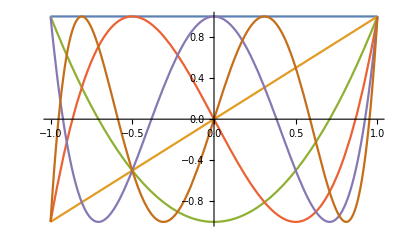

{{π,0,0,0},{0,π/2,0,0},{0,0,π/2,0},{0,0,0,π/2}}

```mathematica
Table[ChebyshevT[n,x],{n,0,5}]
Plot[%,{x,-1,1}]
Table[Integrate[(1-x^2)^(-1/2)ChebyshevT[n,x]ChebyshevT[m,x],{x,-1,1}],{n,0,3},{m,0,3}]
```

```mathematica
$QNMeqn/.r->rh+δr/.f->((#-rh)^γ g[#-rh]&)/.$rh;
"Transform to u: "
{r->rh/u,u∈"[0,1]"} 
$s;
QNMeqn2=L^6 m^(3/2)u^-7 $QNMeqn/.r->rh/u/.f->(#^-4 g[rh/#]&)/.$rh/.q->k π T/.ω->-I λ π T/.T->m^(1/4)/(L π)//Simplify
```

Transform to u:

{r→rh/u,u∈[0,1]}

(k^2 u+16 u^3-5 λ) g[u]+(-5+9 u^4-2 u λ) g'[u]+u (-1+u^4) g''[u]

```mathematica
$M=5;
gsub=g->Function[u,Sum[c[n] ChebyshevT[n,2u-1],{n,0,$M}]]
coeffs=Table[c[n],{n,0,$M}]
```

g→Function[u,∑_(n=0)^($M) c[n] ChebyshevT[n,2 u-1]]

{c[0],c[1],c[2],c[3],c[4],c[5]}

```mathematica
ugrid=Table[1/2(1-Cos[n Pi/$M]),{n,0,$M}]//N
```

{0.,0.0954915,0.345492,0.654508,0.904508,1.}

```mathematica
QNMtrunc=QNMeqn2/.gsub//Simplify
QNMtrunc/.u->ugrid
```

2 (-5+9 u^4-2 u λ) (c[1]+4 (-1+2 u) c[2]+3 (3-16 u+16 u^2) c[3]+4 (4-8 u+8 (-1+2 u)^3) c[4]+5 (1-12 (1-2 u)^2+16 (1-2 u)^4) c[5])+16 u (-1+u^4) (c[2]+6 (-1+2 u) c[3]+20 c[4]-96 u c[4]+96 u^2 c[4]-50 c[5]+420 u c[5]-960 u^2 c[5]+640 u^3 c[5])+(k^2 u+16 u^3-5 λ) (c[0]+(-1+2 u) c[1]+(1-8 u+8 u^2) c[2]+(-1+18 u-48 u^2+32 u^3) c[3]+(1-8 (1-2 u)^2+8 (1-2 u)^4) c[4]+(-5+10 u-20 (-1+2 u)^3+16 (-1+2 u)^5) c[5])

{0.+(0.-5 λ) (c[0]-1. c[1]+1. c[2]-1. c[3]+1. c[4]-1. c[5])-10. (c[1]-4. c[2]+9. c[3]-16. c[4]+25. c[5]),2 (-4.99925-0.190983 λ) (0.+c[1]-3.23607 c[2]+4.8541 c[3]-4. c[4])-1.52774 (c[2]-4.8541 c[3]+11.7082 c[4]-18.0902 c[5])+(0.013932+0.0954915 k^2-5 λ) (c[0]-0.809017 c[1]+0.309017 c[2]+0.309017 c[3]-0.809017 c[4]+1. c[5]),(0.65983+0.345492 k^2-5 λ) (c[0]-0.309017 c[1]-0.809017 c[2]+0.809017 c[3]+0.309017 c[4]-1. c[5])+2 (-4.87177-0.690983 λ) (c[1]-1.23607 c[2]-1.8541 c[3]+4. c[4]-1.249×10^-15 c[5])-5.4491 (c[2]-1.8541 c[3]-1.7082 c[4]+6.90983 c[5]),-8.55039 (c[2]+1.8541 c[3]-1.7082 c[4]-6.90983 c[5])+2 (-3.3484-1.30902 λ) (c[1]+1.23607 c[2]-1.8541 c[3]-4. c[4]-1.249×10^-15 c[5])+(4.48607+0.654508 k^2-5 λ) (c[0]+0.309017 c[1]-0.809017 c[2]-0.809017 c[3]+0.309017 c[4]+1. c[5]),2 (1.02411-1.80902 λ) (0.+c[1]+3.23607 c[2]+4.8541 c[3]+4. c[4])+(11.8402+0.904508 k^2-5 λ) (c[0]+0.809017 c[1]+0.309017 c[2]-0.309017 c[3]-0.809017 c[4]-1. c[5])-4.78527 (c[2]+4.8541 c[3]+11.7082 c[4]+18.0902 c[5]),0.+(16.+1. k^2-5 λ) (c[0]+1. c[1]+1. c[2]+1. c[3]+1. c[4]+1. c[5])+2 (4.-2. λ) (c[1]+4. c[2]+9. c[3]+16. c[4]+25. c[5])}

```mathematica
QNMmtx=Coefficient[#,coeffs]&/@(QNMtrunc/.u->ugrid)
QNMmtx.coeffs-(QNMtrunc/.u->ugrid)//Simplify//Chop
```

{{-5 λ,-10.+5. λ,40.-5. λ,-90.+5. λ,160.-5. λ,-250.+5. λ},{0.013932+0.0954915 k^2-5 λ,-10.0098-0.0772542 k^2+3.66312 λ,30.8324+0.0295085 k^2-0.309017 λ,-41.1137+0.0295085 k^2-3.39919 λ,22.0957-0.0772542 k^2+5.57295 λ,27.651+0.0954915 k^2-5. λ},{0.65983+0.345492 k^2-5 λ,-9.94744-0.106763 k^2+0.163119 λ,6.06076-0.279508 k^2+5.75329 λ,28.7025+0.279508 k^2-1.48278 λ,-29.4621+0.106763 k^2-7.07295 λ,-38.3122-0.345492 k^2+5. λ},{4.48607+0.654508 k^2-5 λ,-5.31054+0.202254 k^2-4.16312 λ,-20.4574-0.529508 k^2+0.809017 λ,-7.06603-0.529508 k^2+8.89919 λ,42.7793+0.202254 k^2+8.92705 λ,63.5678+0.654508 k^2-5. λ},{11.8402+0.904508 k^2-5 λ,11.6271+0.731763 k^2-7.66312 λ,5.50174+0.279508 k^2-13.2533 λ,-16.9447-0.279508 k^2-16.0172 λ,-57.4129-0.731763 k^2-10.4271 λ,-98.4065-0.904508 k^2+5. λ},{16.+1. k^2-5 λ,24.+1. k^2-9. λ,48.+1. k^2-21. λ,88.+1. k^2-41. λ,144.+1. k^2-69. λ,216.+1. k^2-105. λ}}

{0,0,0,0,0,0}

```mathematica
α=QNMmtx/.λ->0
β=-Coefficient[QNMmtx,λ]
```

{{0,-10.,40.,-90.,160.,-250.},{0.013932+0.0954915 k^2,-10.0098-0.0772542 k^2,30.8324+0.0295085 k^2,-41.1137+0.0295085 k^2,22.0957-0.0772542 k^2,27.651+0.0954915 k^2},{0.65983+0.345492 k^2,-9.94744-0.106763 k^2,6.06076-0.279508 k^2,28.7025+0.279508 k^2,-29.4621+0.106763 k^2,-38.3122-0.345492 k^2},{4.48607+0.654508 k^2,-5.31054+0.202254 k^2,-20.4574-0.529508 k^2,-7.06603-0.529508 k^2,42.7793+0.202254 k^2,63.5678+0.654508 k^2},{11.8402+0.904508 k^2,11.6271+0.731763 k^2,5.50174+0.279508 k^2,-16.9447-0.279508 k^2,-57.4129-0.731763 k^2,-98.4065-0.904508 k^2},{16.+1. k^2,24.+1. k^2,48.+1. k^2,88.+1. k^2,144.+1. k^2,216.+1. k^2}}

{{5,-5.,5.,-5.,5.,-5.},{5,-3.66312,0.309017,3.39919,-5.57295,5.},{5,-0.163119,-5.75329,1.48278,7.07295,-5.},{5,4.16312,-0.809017,-8.89919,-8.92705,5.},{5,7.66312,13.2533,16.0172,10.4271,-5.},{5,9.,21.,41.,69.,105.}}

```mathematica
Eigenvalues[{α,β}/.k->0]//Reverse
```

{2.31955-2.20666 ⅈ,2.31955+2.20666 ⅈ,3.26418-0.852315 ⅈ,3.26418+0.852315 ⅈ,1.19905+3.66699 ⅈ,1.19905-3.66699 ⅈ}

```mathematica
Clear[gsub,coeffs,ugrid,M,QNMroots];
gsub[M_]:=g:>Function[u,Sum[c[n] cheby[n,2u-1],{n,0,M}]];
ugrid[M_,prec_]:=Table[1/2(1-Cos[n Pi/M])//N[#,prec]&,{n,0,M}];
coeffs[M_]:=Table[c[n],{n,0,M}];
geneigs[mtx_]:=Eigenvalues[{mtx/.λ->0,-Coefficient[mtx,λ]}]//Reverse;
QNMroots[M_,kk_,prec_:MachinePrecision]:=geneigs[(Coefficient[#,coeffs[M]]&/@((QNMeqn2/.k->kk/.gsub[M]/.u->#)&/@ugrid[M,prec]))/.chebysub];
chebysub={Derivative[0,m_][cheby][n_,u_?NumberQ]->n 2^(m-1)(m-1)!GegenbauerC[n-m,m,u],
cheby[n_,u_?NumberQ]->ChebyshevT[n,u]};
```

```mathematica
QNMroots[5,0]
QNMroots[10,0]
QNMroots[15,0]
QNMroots[20,0]
QNMroots[25,0]
QNMroots[30,0]
QNMroots[35,0]
QNMroots[40,0]
```

{2.31955-2.20666 ⅈ,2.31955+2.20666 ⅈ,3.26418-0.852315 ⅈ,3.26418+0.852315 ⅈ,1.19905+3.66699 ⅈ,1.19905-3.66699 ⅈ}

{2.72974-3.1249 ⅈ,2.72974+3.1249 ⅈ,4.06469+3.41811 ⅈ,4.06469-3.41811 ⅈ,5.41647+0. ⅈ,5.09385-1.9446 ⅈ,5.09385+1.9446 ⅈ,2.84624+5.18343 ⅈ,2.84624-5.18343 ⅈ,1.64033-7.53751 ⅈ,1.64033+7.53751 ⅈ}

{2.7467-3.11945 ⅈ,2.7467+3.11945 ⅈ,4.61134-5.05565 ⅈ,4.61134+5.05565 ⅈ,5.98017-4.46557 ⅈ,5.98017+4.46557 ⅈ,7.39828-1.08969 ⅈ,7.39828+1.08969 ⅈ,6.97439-3.10506 ⅈ,6.97439+3.10506 ⅈ,4.33318+6.64024 ⅈ,4.33318-6.64024 ⅈ,3.45506-8.83787 ⅈ,3.45506+8.83787 ⅈ,2.13706-11.6104 ⅈ,2.13706+11.6104 ⅈ}

{2.74668+3.11945 ⅈ,2.74668-3.11945 ⅈ,4.76414+5.16998 ⅈ,4.76414-5.16998 ⅈ,6.44495+6.58585 ⅈ,6.44495-6.58585 ⅈ,9.53017+0. ⅈ,9.32768-2.24186 ⅈ,9.32768+2.24186 ⅈ,7.98806-5.54074 ⅈ,7.98806+5.54074 ⅈ,8.87683-4.31691 ⅈ,8.87683+4.31691 ⅈ,5.76575+8.11084 ⅈ,5.76575-8.11084 ⅈ,5.04378-10.2321 ⅈ,5.04378+10.2321 ⅈ,4.07096+12.699 ⅈ,4.07096-12.699 ⅈ,2.64613+15.7849 ⅈ,2.64613-15.7849 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76607+7.19914 ⅈ,6.76607-7.19914 ⅈ,8.24153-7.80171 ⅈ,8.24153+7.80171 ⅈ,11.5706-1.1523 ⅈ,11.5706+1.1523 ⅈ,11.2274-3.41634 ⅈ,11.2274+3.41634 ⅈ,7.22446-9.57606 ⅈ,7.22446+9.57606 ⅈ,10.0471-6.58591 ⅈ,10.0471+6.58591 ⅈ,10.7815+5.5952 ⅈ,10.7815-5.5952 ⅈ,6.5584+11.6459 ⅈ,6.5584-11.6459 ⅈ,5.73705-13.9804 ⅈ,5.73705+13.9804 ⅈ,4.67497-16.6772 ⅈ,4.67497+16.6772 ⅈ,3.15485-20.0238 ⅈ,3.15485+20.0238 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76957-7.18791 ⅈ,6.76957+7.18791 ⅈ,8.66936+9.18741 ⅈ,8.66936-9.18741 ⅈ,10.1199-8.80199 ⅈ,10.1199+8.80199 ⅈ,13.7084+0. ⅈ,13.554-2.32965 ⅈ,13.554+2.32965 ⅈ,13.1087+4.59883 ⅈ,13.1087-4.59883 ⅈ,8.67711-10.9969 ⅈ,8.67711+10.9969 ⅈ,12.2117-7.51712 ⅈ,12.2117+7.51712 ⅈ,12.6435-7.01898 ⅈ,12.6435+7.01898 ⅈ,8.04068-13.0665 ⅈ,8.04068+13.0665 ⅈ,7.30503-15.3251 ⅈ,7.30503+15.3251 ⅈ,6.40838+17.842 ⅈ,6.40838-17.842 ⅈ,5.26644-20.7348 ⅈ,5.26644+20.7348 ⅈ,3.65972-24.3074 ⅈ,3.65972+24.3074 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76956+7.18793 ⅈ,6.76956-7.18793 ⅈ,8.77281-9.19706 ⅈ,8.77281+9.19706 ⅈ,10.5043-10.8628 ⅈ,10.5043+10.8628 ⅈ,12.098-9.82422 ⅈ,12.098+9.82422 ⅈ,15.7794+1.13366 ⅈ,15.7794-1.13366 ⅈ,15.4806-3.56173 ⅈ,15.4806+3.56173 ⅈ,10.0862+12.4213 ⅈ,10.0862-12.4213 ⅈ,15.0102-5.74426 ⅈ,15.0102+5.74426 ⅈ,13.9751-8.18313 ⅈ,13.9751+8.18313 ⅈ,14.9431-8.75644 ⅈ,14.9431+8.75644 ⅈ,9.50594-14.4892 ⅈ,9.50594+14.4892 ⅈ,8.82545+16.6991 ⅈ,8.82545-16.6991 ⅈ,8.0254-19.1092 ⅈ,8.0254+19.1092 ⅈ,7.06073-21.7854 ⅈ,7.06073+21.7854 ⅈ,5.84633-24.8504 ⅈ,5.84633+24.8504 ⅈ,4.15992-28.6241 ⅈ,4.15992+28.6241 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76957+7.18793 ⅈ,6.76957-7.18793 ⅈ,8.77257-9.19733 ⅈ,8.77257+9.19733 ⅈ,10.7717+11.2333 ⅈ,10.7717-11.2333 ⅈ,16.536+0. ⅈ,16.1343+3.82854 ⅈ,16.1343-3.82854 ⅈ,14.9371-7.52418 ⅈ,14.9371+7.52418 ⅈ,13.2035+10.9085 ⅈ,13.2035-10.9085 ⅈ,12.6416-12.3248 ⅈ,12.6416+12.3248 ⅈ,11.4989+13.8473 ⅈ,11.4989-13.8473 ⅈ,10.9575+15.9125 ⅈ,10.9575-15.9125 ⅈ,19.7309+2.99979 ⅈ,19.7309-2.99979 ⅈ,16.9974-11.1067 ⅈ,16.9974+11.1067 ⅈ,18.5708-8.47661 ⅈ,18.5708+8.47661 ⅈ,10.3189-18.0891 ⅈ,10.3189+18.0891 ⅈ,9.58277-20.428 ⅈ,9.58277+20.428 ⅈ,8.72371-22.9729 ⅈ,8.72371+22.9729 ⅈ,7.69684-25.7911 ⅈ,7.69684+25.7911 ⅈ,6.4159+29.0108 ⅈ,6.4159-29.0108 ⅈ,4.65546-32.9662 ⅈ,4.65546+32.9662 ⅈ}

```mathematica
QNMroots[20,2]/2
QNMroots[30,2]/2
QNMroots[40,2]/2
QNMroots[50,2]/2
```

{1.26733-1.95433 ⅈ,1.26733+1.95433 ⅈ,2.29762+2.88055 ⅈ,2.29762-2.88055 ⅈ,3.28676+3.42224 ⅈ,3.28676-3.42224 ⅈ,4.90467+0. ⅈ,4.80115-1.1355 ⅈ,4.80115+1.1355 ⅈ,4.08038-2.87604 ⅈ,4.08038+2.87604 ⅈ,2.85909-4.10326 ⅈ,2.85909+4.10326 ⅈ,4.54447-2.17694 ⅈ,4.54447+2.17694 ⅈ,2.51209+5.15318 ⅈ,2.51209-5.15318 ⅈ,2.03039+6.38349 ⅈ,2.03039-6.38349 ⅈ,1.32175-7.92273 ⅈ,1.32175+7.92273 ⅈ}

{1.26733-1.95433 ⅈ,1.26733+1.95433 ⅈ,2.29796-2.88026 ⅈ,2.29796+2.88026 ⅈ,3.31492+3.83663 ⅈ,3.31492-3.83663 ⅈ,4.29869+4.76326 ⅈ,4.29869-4.76326 ⅈ,5.17638-4.49278 ⅈ,5.17638+4.49278 ⅈ,6.97846+0. ⅈ,6.90036+1.17332 ⅈ,6.90036-1.17332 ⅈ,4.33258-5.51855 ⅈ,4.33258+5.51855 ⅈ,6.67653-2.31431 ⅈ,6.67653+2.31431 ⅈ,6.14595-3.90908 ⅈ,6.14595+3.90908 ⅈ,6.41891+3.44774 ⅈ,6.41891-3.44774 ⅈ,4.01177-6.56005 ⅈ,4.01177+6.56005 ⅈ,3.64644+7.6878 ⅈ,3.64644-7.6878 ⅈ,3.20027+8.94462 ⅈ,3.20027-8.94462 ⅈ,2.6311+10.3893 ⅈ,2.6311-10.3893 ⅈ,1.82933+12.1737 ⅈ,1.82933-12.1737 ⅈ}

{1.26733+1.95433 ⅈ,1.26733-1.95433 ⅈ,2.29796-2.88026 ⅈ,2.29796+2.88026 ⅈ,3.31491-3.83663 ⅈ,3.31491+3.83663 ⅈ,4.3258-4.80745 ⅈ,4.3258+4.80745 ⅈ,5.32148-5.7897 ⅈ,5.32148+5.7897 ⅈ,7.793-3.5999 ⅈ,7.793+3.5999 ⅈ,6.78146-5.32762 ⅈ,6.78146+5.32762 ⅈ,8.54903-1.76511 ⅈ,8.54903+1.76511 ⅈ,8.78016+0. ⅈ,6.30535-6.29804 ⅈ,6.30535+6.29804 ⅈ,5.74679-6.94751 ⅈ,5.74679+6.94751 ⅈ,5.47128-7.97623 ⅈ,5.47128+7.97623 ⅈ,9.53621+1.63873 ⅈ,9.53621-1.63873 ⅈ,8.37061-5.59453 ⅈ,8.37061+5.59453 ⅈ,9.16868-4.41151 ⅈ,9.16868+4.41151 ⅈ,5.15359-9.06452 ⅈ,5.15359+9.06452 ⅈ,4.78701-10.2331 ⅈ,4.78701+10.2331 ⅈ,4.35872+11.5046 ⅈ,4.35872-11.5046 ⅈ,3.84636+12.9127 ⅈ,3.84636-12.9127 ⅈ,3.20683-14.5214 ⅈ,3.20683+14.5214 ⅈ,2.32749-16.498 ⅈ,2.32749+16.498 ⅈ}

{1.26733+1.95433 ⅈ,1.26733-1.95433 ⅈ,2.29796-2.88026 ⅈ,2.29796+2.88026 ⅈ,3.31491+3.83663 ⅈ,3.31491-3.83663 ⅈ,4.32563-4.80741 ⅈ,4.32563+4.80741 ⅈ,7.52568+0. ⅈ,7.39552+1.64913 ⅈ,7.39552-1.64913 ⅈ,7.00382+3.26498 ⅈ,7.00382-3.26498 ⅈ,5.30395+5.75574 ⅈ,5.30395-5.75574 ⅈ,6.35592-4.83198 ⅈ,6.35592+4.83198 ⅈ,5.78685-6.46161 ⅈ,5.78685+6.46161 ⅈ,5.95407+7.45932 ⅈ,5.95407-7.45932 ⅈ,6.21804+8.47729 ⅈ,6.21804-8.47729 ⅈ,6.44969-9.45953 ⅈ,6.44969+9.45953 ⅈ,6.49714+10.477 ⅈ,6.49714-10.477 ⅈ,6.28206+11.5951 ⅈ,6.28206-11.5951 ⅈ,8.10108-10.5669 ⅈ,8.10108+10.5669 ⅈ,5.92961+12.7844 ⅈ,5.92961-12.7844 ⅈ,10.8781-10.1103 ⅈ,10.8781+10.1103 ⅈ,5.51291+14.0638 ⅈ,5.51291-14.0638 ⅈ,13.5848-8.71633 ⅈ,13.5848+8.71633 ⅈ,5.03152-15.452 ⅈ,5.03152+15.452 ⅈ,15.8967+6.02623 ⅈ,15.8967-6.02623 ⅈ,17.307-2.16604 ⅈ,17.307+2.16604 ⅈ,4.46328+16.984 ⅈ,4.46328-16.984 ⅈ,3.7637+18.7284 ⅈ,3.7637-18.7284 ⅈ,2.8168-20.8657 ⅈ,2.8168+20.8657 ⅈ}

```mathematica
QNMroots[20,2,30]/2
QNMroots[30,2,30]/2
QNMroots[40,2,30]/2
QNMroots[50,2,30]/2
```

{1.26732727539794909501493-1.95433087146849939403639 ⅈ,1.26732727539794909501493+1.95433087146849939403639 ⅈ,2.29761756685275515093336-2.88055122207291754672557 ⅈ,2.29761756685275515093336+2.88055122207291754672557 ⅈ,3.28676434116845335401791-3.42223653431144000124448 ⅈ,3.28676434116845335401791+3.42223653431144000124448 ⅈ,4.90466835715088471396312,4.80114616098510634137391-1.13550143915216746267978 ⅈ,4.80114616098510634137391+1.13550143915216746267978 ⅈ,4.08038070680847678643255+2.87603944605452928566832 ⅈ,4.08038070680847678643255-2.87603944605452928566832 ⅈ,2.85908821355954298193676-4.10325841764087695087471 ⅈ,2.85908821355954298193676+4.10325841764087695087471 ⅈ,4.54446693516245840068674-2.17694126979147269867136 ⅈ,4.54446693516245840068674+2.17694126979147269867136 ⅈ,2.51209356565227021831607-5.15318262572532319104793 ⅈ,2.51209356565227021831607+5.15318262572532319104793 ⅈ,2.03039029217053862928468-6.38349038394510046739998 ⅈ,2.03039029217053862928468+6.38349038394510046739998 ⅈ,1.32175033069290950218924-7.92273092096611108343867 ⅈ,1.32175033069290950218924+7.92273092096611108343867 ⅈ}

{1.26732726341707022709571-1.95433088379041284579575 ⅈ,1.26732726341707022709571+1.95433088379041284579575 ⅈ,2.29795704580093138202795-2.88026256539204171109936 ⅈ,2.29795704580093138202795+2.88026256539204171109936 ⅈ,3.3149214275881362320001-3.83663374715934510837485 ⅈ,3.3149214275881362320001+3.83663374715934510837485 ⅈ,4.29868897203904364094865-4.76326229245926411731277 ⅈ,4.29868897203904364094865+4.76326229245926411731277 ⅈ,5.17640457243705272614907-4.49275552765307162808003 ⅈ,5.17640457243705272614907+4.49275552765307162808003 ⅈ,6.97832850856632290729225,6.90047752634971414497686-1.17335992617744338759073 ⅈ,6.90047752634971414497686+1.17335992617744338759073 ⅈ,4.33257752582161683271013-5.51855685696722351569382 ⅈ,4.33257752582161683271013+5.51855685696722351569382 ⅈ,6.67642237558874484542821-2.3142467052385892304666 ⅈ,6.67642237558874484542821+2.3142467052385892304666 ⅈ,6.14583557497189210274538-3.90908788002427715958766 ⅈ,6.14583557497189210274538+3.90908788002427715958766 ⅈ,6.41906630415306720734091-3.44777754366724460507136 ⅈ,6.41906630415306720734091+3.44777754366724460507136 ⅈ,4.01177118168848649999511-6.56004997171867056358655 ⅈ,4.01177118168848649999511+6.56004997171867056358655 ⅈ,3.64644404726185372615092-7.6877959604241052535309 ⅈ,3.64644404726185372615092+7.6877959604241052535309 ⅈ,3.20026863249551252201408-8.94461737567688882516876 ⅈ,3.20026863249551252201408+8.94461737567688882516876 ⅈ,2.63109908459046696624944-10.3892530498275681127835 ⅈ,2.63109908459046696624944+10.3892530498275681127835 ⅈ,1.82933317386237577407388-12.1737167197133827679339 ⅈ,1.82933317386237577407388+12.1737167197133827679339 ⅈ}

{1.26732726341706410285085-1.95433088379042054659143 ⅈ,1.26732726341706410285085+1.95433088379042054659143 ⅈ,2.29795704651987263755697-2.88026256484964260639559 ⅈ,2.29795704651987263755697+2.88026256484964260639559 ⅈ,3.31490716032855514556195-3.83663222293320737893068 ⅈ,3.31490716032855514556195+3.83663222293320737893068 ⅈ,4.32587111939003429551884-4.80739193756078967171886 ⅈ,4.32587111939003429551884+4.80739193756078967171886 ⅈ,5.33221413277099184042022-5.7881080772495501073425 ⅈ,5.33221413277099184042022+5.7881080772495501073425 ⅈ,6.23194099793305973054509+6.16849707769900431021922 ⅈ,6.23194099793305973054509-6.16849707769900431021922 ⅈ,7.12005200567218969490657-5.5016151186086196449163 ⅈ,7.12005200567218969490657+5.5016151186086196449163 ⅈ,5.74646167539594221332271-6.96831223777301132714608 ⅈ,5.74646167539594221332271+6.96831223777301132714608 ⅈ,9.06538064548302058265807,9.00384931924750504514584-1.19449118405738807003274 ⅈ,9.00384931924750504514584+1.19449118405738807003274 ⅈ,8.82313180810857460692574-2.36582564173018046870326 ⅈ,8.82313180810857460692574+2.36582564173018046870326 ⅈ,8.52973800537671901718509-3.49668895118990730854232 ⅈ,8.52973800537671901718509+3.49668895118990730854232 ⅈ,8.04101818195526317377824-4.64641060233684842092459 ⅈ,8.04101818195526317377824+4.64641060233684842092459 ⅈ,5.47262157812776319293572-7.97720442931653159505922 ⅈ,5.47262157812776319293572+7.97720442931653159505922 ⅈ,8.60004840342213326724092-5.0979365703575990858546 ⅈ,8.60004840342213326724092+5.0979365703575990858546 ⅈ,5.1537153278543227534375-9.06449423533830060645489 ⅈ,5.1537153278543227534375+9.06449423533830060645489 ⅈ,4.78701239261060995396637-10.2330855128271748561702 ⅈ,4.78701239261060995396637+10.2330855128271748561702 ⅈ,4.35871782515072154066524-11.5045576861686066798277 ⅈ,4.35871782515072154066524+11.5045576861686066798277 ⅈ,3.8463563732010344227409-12.9126675154174256133618 ⅈ,3.8463563732010344227409+12.9126675154174256133618 ⅈ,3.20682844844889005523563-14.5214170021390225642655 ⅈ,3.20682844844889005523563+14.5214170021390225642655 ⅈ,2.32749050995697764350418-16.4979880731192637667881 ⅈ,2.32749050995697764350418+16.4979880731192637667881 ⅈ}

{1.2673272634170641028504-1.9543308837904205465965 ⅈ,1.2673272634170641028504+1.9543308837904205465965 ⅈ,2.2979570465198732580397-2.8802625648496418618889 ⅈ,2.2979570465198732580397+2.8802625648496418618889 ⅈ,3.31490716028999410921-3.8366322229339033238867 ⅈ,3.31490716028999410921+3.8366322229339033238867 ⅈ,4.3258713695497287327082-4.8073923430520995115796 ⅈ,4.3258713695497287327082+4.8073923430520995115796 ⅈ,5.3336221975535519220457-5.7861818912709116150608 ⅈ,5.3336221975535519220457+5.7861818912709116150608 ⅈ,6.3395117553496663341352-6.7699664849888459193064 ⅈ,6.3395117553496663341352+6.7699664849888459193064 ⅈ,7.2891201724253418070117-7.6436358931136996424779 ⅈ,7.2891201724253418070117+7.6436358931136996424779 ⅈ,8.1476244454176590960422+7.2074124688846377112796 ⅈ,8.1476244454176590960422-7.2074124688846377112796 ⅈ,7.1866218365554651454854-8.370018298292127177804 ⅈ,7.1866218365554651454854+8.370018298292127177804 ⅈ,9.0612813129323656726078-6.5129292089898935022217 ⅈ,9.0612813129323656726078+6.5129292089898935022217 ⅈ,11.159871053219510341347,11.108984817268606675074-1.2081126953137639077289 ⅈ,11.108984817268606675074+1.2081126953137639077289 ⅈ,10.958590804337400716425-2.4003077953881611219491 ⅈ,10.958590804337400716425+2.4003077953881611219491 ⅈ,10.715319750572887863788-3.5615222737245136798485 ⅈ,10.715319750572887863788+3.5615222737245136798485 ⅈ,10.383117598569138886099-4.6736300751282935387398 ⅈ,10.383117598569138886099+4.6736300751282935387398 ⅈ,9.8736698399962991607443-5.694692534844316142132 ⅈ,9.8736698399962991607443+5.694692534844316142132 ⅈ,6.9194848565687035645115-9.3990239853311032730451 ⅈ,6.9194848565687035645115+9.3990239853311032730451 ⅈ,6.625520993493094136787-10.463753513702579864319 ⅈ,6.625520993493094136787+10.463753513702579864319 ⅈ,10.955917286813711469537-6.5056149972380351788201 ⅈ,10.955917286813711469537+6.5056149972380351788201 ⅈ,6.2981674545244864756512-11.588050634927493026915 ⅈ,6.2981674545244864756512+11.588050634927493026915 ⅈ,5.930442939843775141294-12.783002271964244293096 ⅈ,5.930442939843775141294+12.783002271964244293096 ⅈ,5.5128969404888024452163-14.06366902269840460516 ⅈ,5.5128969404888024452163+14.06366902269840460516 ⅈ,5.0315193601522567500402-15.452041926202420740522 ⅈ,5.0315193601522567500402+15.452041926202420740522 ⅈ,4.4632752538111981233638-16.983984248800832200989 ⅈ,4.4632752538111981233638+16.983984248800832200989 ⅈ,3.763699819521768843262-18.728362287602982932335 ⅈ,3.763699819521768843262+18.728362287602982932335 ⅈ,2.8168022730823911457264-20.865663579304468771443 ⅈ,2.8168022730823911457264+20.865663579304468771443 ⅈ}